## Imports

```mathematica
(*
examples=Transpose[Import["C:\\Users\\Sam\\Documents\\MATLAB\\KolmogorovDefects\\src\\pSel.mat"][[2]],{3,2,4,1}];
examples//TensorDimensions
denseExamples=Take[examples,100];
Export["denseExamples.txt",Compress[denseExamples]]
*)

ByteCount@denseExamples
denseExamples//TensorDimensions
```

158215264

{100,128,128,2}

```mathematica
Dynamic[{MemoryAvailable[],MemoryInUse[]}]
```

## discrete FFT derivative functions

```mathematica
fftID2=Table[If[x^2+y^2==0,0,-1/(x^2+y^2)],{x,0,128-1},{y,0,128-1}];
fftDx=Table[I x,{x,0,128-1},{y,0,128-1}];
fftDy=Table[I y,{x,0,128-1},{y,0,128-1}];
streamFuncDiscrete[ex_]:=Transpose@Re@InverseFourier[-fftID2 Fourier[Re@InverseFourier[Fourier[ex[[;;,;;,2]]] fftDx]-Re@InverseFourier[Fourier[ex[[;;,;;,1]]] fftDy]]]
discreteDxx[ex_]:=Transpose@Re@InverseFourier[fftDx fftDx Fourier[ex]];
discreteDyy[ex_]:=Transpose@Re@InverseFourier[fftDy fftDy Fourier[ex]];
discreteDxy[ex_]:=Transpose@Re@InverseFourier[fftDx fftDy Fourier[ex]];
discreteHess[ex_,pt_]:={{Extract[discreteDxx[ex],pt],Extract[discreteDxy[ex],pt]},{Extract[discreteDxy[ex],pt],Extract[discreteDyy[ex],pt]}}
Clear[discreteToInterp]
discreteToInterp[dis_]:=discreteToInterp[dis]=ListInterpolation[dis,{{0,2Pi},{0,2Pi}}][Mod[x,2Pi],Mod[y,2Pi]];
skewDiscrete[l_]:=Map[{-#[[2]],#[[1]]}&,l,{2}];
```

```mathematica
activeExample=denseExamples[[15]];
```

```mathematica
Clear[psiInt]
psi=streamFuncDiscrete[activeExample];
absMin=Position[psi,Min[psi]][[1]](2Pi/128)//N
absMax=Position[psi,Max[psi]][[1]](2Pi/128)//N
psiInt=discreteToInterp[psi];
sols=NDSolveValue[{{px'[t],py'[t]}==Grad[psiInt[x,y],{x,y}]/.{x->px[t],y->py[t]},{px[0],py[0]}==absMin},{px[t],py[t]},{t,0,0.3}]
Mod[sols/.t->0.3,2Pi]
```

{3.33794,1.1781}

{0.981748,4.36878}

NDSolveValue::derarg: The derivative operator Derivative[1,0] in («1»)^(1,0)[px[t],py[t]] should act on the pure function.

NDSolveValue[{{px'[t],py'[t]}=={(InterpolatingFunction[…][Mod[px[t],2 π],Mod[py[t],2 π]])^(1,0)[px[t],py[t]]+((1-(Piecewise[{{0, px[t]/(2 π)>Floor[px[t]/(2 π)]}, {Indeterminate, True}}])) InterpolatingFunction[…][Mod[px[t],2 π],Mod[py[t],2 π]])[px[t],py[t]],(InterpolatingFunction[…][Mod[px[t],2 π],Mod[py[t],2 π]])^(0,1)[px[t],py[t]]+((1-(Piecewise[{{0, py[t]/(2 π)>Floor[py[t]/(2 π)]}, {Indeterminate, True}}])) InterpolatingFunction[…][Mod[px[t],2 π],Mod[py[t],2 π]])[px[t],py[t]]},{px[0],py[0]}=={3.33794,1.1781}},{px[t],py[t]},{t,0,0.3}]

NDSolveValue::dsvar: 0.3 cannot be used as a variable.

Mod[NDSolveValue[{{px'[0.3],py'[0.3]}=={(InterpolatingFunction[…][Mod[px[0.3],2 π],Mod[py[0.3],2 π]])^(1,0)[px[0.3],py[0.3]]+((1-(Piecewise[{{0, px[0.3]/(2 π)>Floor[px[0.3]/(2 π)]}, {Indeterminate, True}}])) InterpolatingFunction[…][Mod[px[0.3],2 π],Mod[py[0.3],2 π]])[px[0.3],py[0.3]],(InterpolatingFunction[…][Mod[px[0.3],2 π],Mod[py[0.3],2 π]])^(0,1)[px[0.3],py[0.3]]+((1-(Piecewise[{{0, py[0.3]/(2 π)>Floor[py[0.3]/(2 π)]}, {Indeterminate, True}}])) InterpolatingFunction[…][Mod[px[0.3],2 π],Mod[py[0.3],2 π]])[px[0.3],py[0.3]]},{px[0],py[0]}=={3.33794,1.1781}},{px[0.3],py[0.3]},{0.3,0,0.3}],2 π]

```mathematica
(*allPsi=ParallelMap[streamFuncDiscrete,examples];*)
```

```mathematica
allPsi
```

$Aborted[]

```mathematica
manyPsi=ParallelMap[streamFuncDiscrete,denseExamples];
```

```mathematica
(*Export["manyPsi.txt",Compress[manyPsi]]*)
manyPsiUnc=Uncompress@Import["manyPsi.txt"];
```

```mathematica
normalized=Min[#]+#&/@allPsiUnc;
restFramed=RotateLeft[#,Position[#,Min[#]][[1]]]&/@normalized;
Export["restFramed.txt",Compress[restFramed]]
%//TensorDimensions
```

restFramed.txt

TensorDimensions[restFramed.txt]

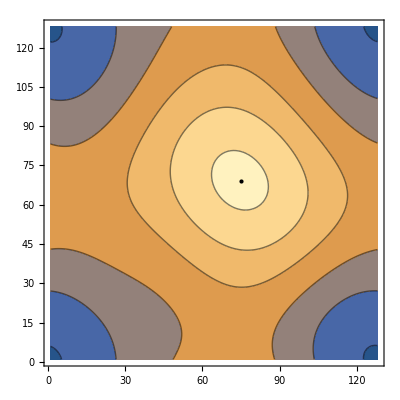

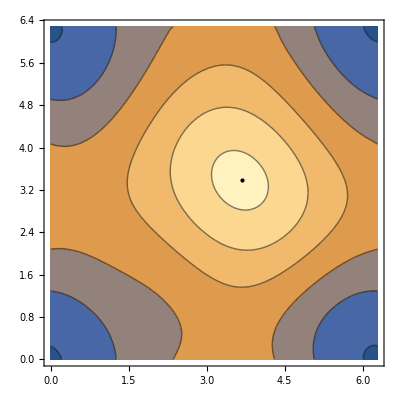

13.3206

-586699.

```mathematica
Show[ListContourPlot[Transpose@#,PerformanceGoal->"Quality"],Graphics[Point[Position[#,Max[#]][[1]]]]]&@restFramed[[3]]
Show[ContourPlot[discreteToInterp[#],{x,0,2Pi},{y,0,2Pi}],Graphics[Point[(2Pi/128)Position[#,Max[#]][[1]]]]]&@restFramed[[3]]
Extract[discreteDxx[#],Position[#,Max[#]][[1]]]&@restFramed[[3]]//Abs//Log
Extract[discreteDyy[#],Position[#,Max[#]][[1]]]&@restFramed[[3]]
```

```mathematica
drawDiagram[xs_]:=Module[{cp,maxCoord,maxPt,elp,xxStr,yyStr,magn,hessEigs},
cp=ListContourPlot[Transpose[xs],PerformanceGoal->"Quality",PlotLabel->"Stream function contour plot, rest frame of minimum"];
maxCoord=Position[xs,Max[xs]][[1]];
maxPt=Graphics[Point[maxCoord]];
hessEigs=Eigensystem@discreteHess[xs,maxCoord]//EchoLabel["eigs"];
xxStr=-Extract[discreteDxx[xs],maxCoord];
yyStr=-Extract[discreteDyy[xs],maxCoord];
magn=Graphics[Text[StringForm["ν = ``",Log@Det@discreteHess[xs,maxCoord]],maxCoord+{0,5}]];
elp=ParametricPlot[(Cos[t]hessEigs[[2]][[1]]+Sin[t]hessEigs[[2]][[2]])15+maxCoord,{t,0,2Pi}];
(*elp=Graphics[{FaceForm[None],EdgeForm[{Thick,Blue}],Rotate[Ellipsoid[maxCoord,0.05Sqrt@Abs@hessEigs[[1]]],ArcTan@@First[hessEigs[[2]]]]}];*)
Image@Show[cp,maxPt,elp,magn]
]
getReducedData[xs_]:=Module[{maxCoord,xxStr,yyStr},
maxCoord=Position[xs,Max[xs]][[1]];
xxStr=-Extract[discreteDxx[xs],maxCoord];
yyStr=-Extract[discreteDyy[xs],maxCoord];
{maxCoord,xxStr,yyStr}
]
getReducedData[restFramed[[1]]]
```

{{74,69},633866.,585505.}

```mathematica
drawDiagram[restFramed[[150]]]
```

eigs  {{-769829.,-476994.},{{-0.728771,-0.684757},{0.684757,-0.728771}}}

-Graphics-

```mathematica
frames=ParallelMap[drawDiagram,restFramed];
```

```mathematica
Export["rotatingElp.gif",frames,AnimationRepetitions->∞,"DisplayDurations"->0.2]
```

restFrameMinDenseElp.gif

```mathematica
trainingData=ParallelMap[getReducedData,restFramed];
```

```mathematica
Export["trainingData.txt",Compress[trainingData]]
```

trainingData.txt

1068

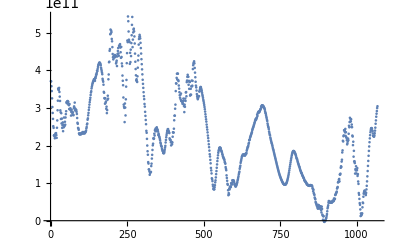

```mathematica
trainingCoords=#[[1]]&/@trainingData;
trainingMagn=#[[2]]#[[3]]&/@trainingData;
ListPlot[trainingMagn]
```

```mathematica
predictor=Predict[trainingCoords->trainingMagn]
%[{80,80}]
```

PredictorFunction[…]

4.55168×10^11

```mathematica
ListPlot3D[Table[predictor[{x,y}]/(10*^11),{x,1,128},{y,1,128}]]
```

-Graphics3D-

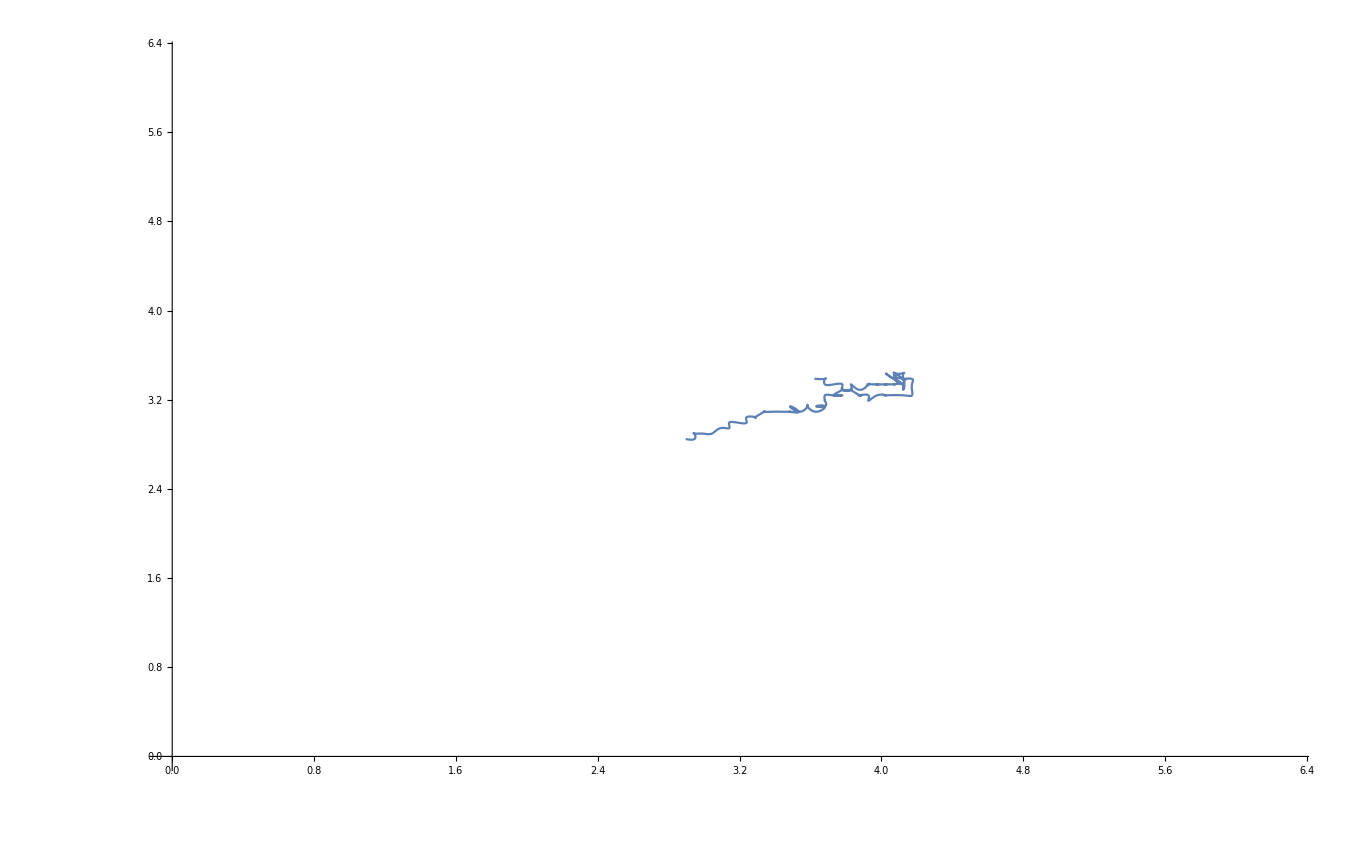

```mathematica
maxPositions=(2Pi/128)Position[#,Max[#]][[1]]&/@restFramed;
ListLinePlot[maxPositions,PlotRange->{{0,2Pi},{0,2Pi}},InterpolationOrder->3]
```

```mathematica
Predict
```